Linear stability analysis of the homogeneous steady state [gray regions in Fig. 10(a,b)];
This notebook uses (n,η) variables instead of (ρ,η).

```mathematica
f=η-n^3+n;
source=p-n;
fTot={f,source,0};(*change depending on source being in u or v*)
```

```mathematica
fixedParams={Du->1,p->-0.2,L->10};
```

### Fixed point

```mathematica
fp=First@Solve[Thread[{f,-f}+eps fTot[[2;;]]==0]/.{n->(u+v),η->(v+Du/Dv u)},{u,v}]
```

{u→-(Dv (-2 p+p^3))/(-Du+Dv),v→(p (Du+Dv-Dv p^2))/(Du-Dv)}

### Jacobian

q2 stands for q^2

```mathematica
jac=(DiagonalMatrix[{-Du q2,-Dv q2}]+D[({f,-f}+eps fTot[[2;;]])/.{n->(u+v),η->(v+Du/Dv u)},{{u,v}}])/.fp;
jac//MatrixForm
```

(1+Du/Dv-eps-3 ((p (Du+Dv-Dv p^2))/(Du-Dv)-(Dv (-2 p+p^3))/(-Du+Dv))^2-Du q2 | 2-eps-3 ((p (Du+Dv-Dv p^2))/(Du-Dv)-(Dv (-2 p+p^3))/(-Du+Dv))^2
-1-Du/Dv+3 ((p (Du+Dv-Dv p^2))/(Du-Dv)-(Dv (-2 p+p^3))/(-Du+Dv))^2 | -2+3 ((p (Du+Dv-Dv p^2))/(Du-Dv)-(Dv (-2 p+p^3))/(-Du+Dv))^2-Dv q2)

Find the edges of the band of unstable modes:

```mathematica
unstableBand=q2/.Solve[Eigenvalues[jac][[2]]==0,q2];
```

### Stability threshold on infinite domain

Find onset where unstable band emerges;
assure that the band lies at positive q^2

```mathematica
epsC=Assuming[{unstableBand[[1]]>0,unstableBand[[2]]>0,eps>0},eps/.Solve[Evaluate[unstableBand[[1]]==unstableBand[[2]]],eps]]
```

{ConditionalExpression[(-2 Du^2+Du Dv+Dv^2+3 Du Dv p^2-3 Dv^2 p^2)/Dv^2-(2 √(Du^4-Du^3 Dv-Du^2 Dv^2+Du Dv^3-3 Du^3 Dv p^2+6 Du^2 Dv^2 p^2-3 Du Dv^3 p^2))/Abs[Dv]^2, ],ConditionalExpression[(-2 Du^2+Du Dv+Dv^2+3 Du Dv p^2-3 Dv^2 p^2)/Dv^2+(2 √(Du^4-Du^3 Dv-Du^2 Dv^2+Du Dv^3-3 Du^3 Dv p^2+6 Du^2 Dv^2 p^2-3 Du Dv^3 p^2))/Abs[Dv]^2, ]}

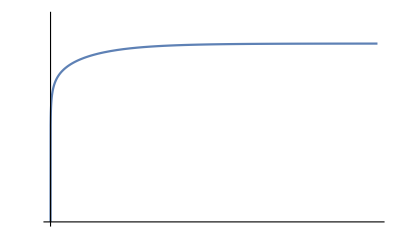

```mathematica
LogLogPlot[Evaluate[epsC/.fixedParams],{Dv,1,10^6},
PlotRange->{10^-7,10},
Ticks->{{{1,},{10^6,}},{{10^-7,},{10^0,}}}]
```